## Prologue

```mathematica
A tangent vector to a curve is a vector that points in the instantaneous direction of motion along the curve . How you find it depends on how the curve is given . Below are the standard methods and quick recipes . Parametric curve r (t)
-Given : r (t) = (x (t), y (t), z (t)) for t in an interval . -Tangent vector : r′ (t) = (x′ (t), y′ (t), z′ (t)) . -Unit tangent : T (t) = r′ (t)/ || r′ (t) || provided r′ (t) != 0.
-Example : r (t) = (t, t^2, ln t) ⇒ tangent r′ (t) = (1, 2 t, 1/t) . Explicit planar curve y = f (x)
-Treat x as parameter : r (x) = (x, f (x)) . -Tangent vector : r′ (x) = (1, f′ (x)) . Any nonzero scalar multiple is also a tangent vector . -Unit tangent : T (x) = (1, f′ (x))/sqrt (1 + (f′ (x))^2) . -Slope form : derivative f′ (x) gives the slope of the tangent line . Implicit curve F (x, y) = 0 (planar)
-If ∂F/∂y != 0, use implicit differentiation : dy/dx = -F_x/F_y . -Tangent vector : (1, dy/dx) or any scalar multiple (F_y, -F_x) (this is perpendicular to gradient ∇F = (F_x, F_y), so tangent) . -Example : circle x^2 + y^2 − 1 = 0 ⇒ ∇F = (2 x, 2 y), tangent vector = (2 y, −2 x) ∝ (y, −x) . Level surface/surface intersection in R^3
-For surface S defined by G (x, y, z) = 0, tangent plane at p has normal ∇G (p) . -Tangent vectors are any vectors v with ∇G (p)·v = 0.
-For a curve given as intersection of two surfaces G1 = 0 and G2 = 0, tangent direction is ∇G1*∇G2 (cross product) evaluated at the point (if nonzero) . Parametrized implicitly in higher dimensions or by constraint
-For curve γ (t) implicitly constrained by constraints, differentiate constraints and solve linear system for γ′ (t) . -For example mechanical linkages : differentiate constraint equations to obtain velocity (tangent) vectors . Practical notes and pitfalls
-If r′ (t) = 0 at a point, first nonzero higher derivative may indicate direction (use Taylor expansion or reparametrization)—the point can be a cusp or stationary point . -Tangent lines use point p = r (t0) and direction r′ (t0) : line L (s) = p + s r′ (t0) . -Unit tangent and curvature : curvature uses T′ (t) normalized; if only direction needed, any nonzero scalar multiple of r′ is sufficient . Summary formulas

Parametric : tangent = r′ (t) . Explicit y = f (x) : tangent = (1, f′ (x)). Implicit F (x, y) = 0 : tangent = (F_y, −F_x) or (1, −F_x/F_y). 
(* https://www.quora.com/How-do-you-find-a-tangent-vector-to-a-curve *)
```

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;Clear[i,κr,κi];rep={a->Subscript[a, 1],a2->Subscript[a, 2],κi->Subscript[κ, i],κr->Subscript[κ, r], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b->Subscript[b, 1],a1->Subscript[a, 1]};
ass=Assumptions->{ξ,vz,vp,ky,kz,ek,b,κi,κr}∈ Reals &&  k>0 && kp>0 && ek>0 && vp>0 && vz>0;
sx=({{0, 1}, {1, 0}});sy=({{0, -ⅈ}, {ⅈ, 0}});sz=({{1, 0}, {0, -1}});
id=({{1, 0}, {0, 1}});
Clear[vp,vz,dx,dy,dz];{dx,dy,dz}={2 vp vz kz kx χ,2 vp vz kz ky χ,vp^2(kx^2+ky^2)-vz^2 kz^2};
```

```mathematica
(****** 2-band Berrry-dipole node with quad disp. *)
Clear[ham,eval,χ,vp];
ham=dx sx+dy sy+dz sz;
FullSimplify[Eigensystem[ham]/. χ^2->1,ass]
dx sxψ+dy syψ+dz szψ/.{kx->-ⅈ Dx}//FullSimplify
```

{{-((kx^2+ky^2) vp^2)-kz^2 vz^2,(kx^2+ky^2) vp^2+kz^2 vz^2},{{-(kz vz)/(kx vp+ⅈ ky vp),1},{((kx-ⅈ ky) vp)/(kz vz),1}}}

(-Dx^2+ky^2) szψ vp^2-2 ⅈ Dx kz sxψ vp vz+2 ky kz syψ vp vz-kz^2 szψ vz^2

## Single Node

```mathematica
Clear[κ,κi,κr,eq0,a,b,vp,vz];χ=1;
κ=κr+κi;
ψ={1,a+ⅈ b};
ψdag={1,a-ⅈ b};
eq0=2FullSimplify[  κi ψdag.( sz.ψ) vp^2+ kz ψdag.(sx.ψ) vp χ,ass]/(2vp)
Solve[eq0==0,κi]
dx sxψ+dy syψ+dz szψ/.{kx->-ⅈ Dx}//FullSimplify
```

2 a kz-(-1+a^2+b^2) vp κi

{{κi→(2 a kz)/((-1+a^2+b^2) vp)}}

(-Dx^2+ky^2) szψ vp^2-2 ⅈ Dx kz sxψ vp vz+2 ky kz syψ vp vz-kz^2 szψ vz^2

```mathematica
Clear[en,eq,eqn];(*κi=(2 a kz)/((-1+a^2+b^2) vp);*)
χ=1;κ=κr+κi;
eq=FullSimplify[(-κ^2+ky^2) sz.ψ vp^2-kz^2 vz^2 sz.ψ+2 kz (ⅈ κ sx.ψ+ky sy.ψ) vp vz χ-en id.ψ]
eqn=FullSimplify[Flatten[ComplexExpand[ReIm[eq]],1],ass]
solu=FullSimplify[Solve[eq0==0 && eqn[[1]]==0 && eqn[[2]]==0 eqn[[3]]==0 &&eqn[[4]]==0 && κr≠ 0 ,{en,κr,κi,a,b}],ass]
Clear[κ,κi,κr,a,b];
```

{-en-kz^2 vz^2+2 (-ⅈ a+b) kz vp vz (ky-κi-κr)+vp^2 (ky^2-(κi+κr)^2),-((a+ⅈ b) en)+(a+ⅈ b) kz^2 vz^2+2 ⅈ kz vp vz (ky+κi+κr)+(-a-ⅈ b) vp^2 (ky^2-(κi+κr)^2)}

{-en+ky^2 vp^2+2 b ky kz vp vz-kz^2 vz^2-2 b kz vp vz (κi+κr)-vp^2 (κi+κr)^2,2 a kz vp vz (-ky+κi+κr),a (-en-ky^2 vp^2+kz^2 vz^2+vp^2 (κi+κr)^2),2 kz vp vz (ky+κi+κr)+b (-en-ky^2 vp^2+kz^2 vz^2+vp^2 (κi+κr)^2)}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→-2 ky kz vp vz,κr→-ky+(kz vz)/vp-κi,a→0,b→-1},{en→-2 ky kz vp vz,κr→ky+(kz vz)/vp-κi,a→0,b→-1},{en→2 ky kz vp vz,κr→-(kz vz+vp (ky+κi))/vp,a→0,b→1},{en→2 ky kz vp vz,κr→ky-(kz vz)/vp-κi,a→0,b→1},{en→-kz^2 vz^2,κr→ky-κi,a→(kz^3 vz-√(-4 ky^2 vp^4 κi^2+kz^2 vz^2 (kz^2+vp^2 κi^2)) Abs[kz])/(kz^2 vp vz κi),b→-(2 ky vp)/(kz vz)},{en→-kz^2 vz^2,κr→ky-κi,a→(kz^3 vz+√(-4 ky^2 vp^4 κi^2+kz^2 vz^2 (kz^2+vp^2 κi^2)) Abs[kz])/(kz^2 vp vz κi),b→-(2 ky vp)/(kz vz)},{en→(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2,κr→ky-(kz vz)/(b vp),κi→0,a→0},{en→kz vz (2 b ky vp+(-1+b^2) kz vz),κr→-(ky vp+b kz vz)/vp,κi→0,a→0},{en→-kz^2 vz^2,κr→-ky,κi→0,a→0,b→0},{en→-kz^2 vz^2,κr→ky,κi→0,a→0,b→-(2 ky vp)/(kz vz)}}

```mathematica
(* where κr vanishes, what is the energy value? 
{en->kz vz (2 b ky vp+(-1+b^2) kz vz),κr->-(ky vp+b kz vz)/vp,κi->0,a->0} *)
enfa=kz vz (2 b ky vp+(-1+b^2) kz vz);
soll=FullSimplify[Solve[ky^2 vp^2+kz^2 vz^2==μ && 0==-(ky vp+b kz vz)/vp,{ky,kz}],ass]
FullSimplify[kz vz (2 b ky vp+(-1+b^2) kz vz)/.soll,ass](* this is the right energy solution for μ<0*)
(* {en->(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2,κr->ky-(kz vz)/(b vp),κi->0,a->0}*)
soll=FullSimplify[Solve[ky^2 vp^2+kz^2 vz^2==μ && 0==ky-(kz vz)/(b vp),{ky,kz}],ass]
FullSimplify[(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2/.soll,ass](* this is the right solution for μ>0 *)
```

{{ky→(b √(μ/(1+b^2)))/vp,kz→-√(μ/((1+b^2) vz^2))},{ky→-(b √(μ/(1+b^2)))/vp,kz→√(μ/((1+b^2) vz^2))}}

{-μ,-μ}

{{ky→-√(μ/((1+b^2) vp^2)),kz→-(b √(μ/(1+b^2)))/vz},{ky→√(μ/((1+b^2) vp^2)),kz→(b √(μ/(1+b^2)))/vz}}

{μ,μ}

```mathematica
mu=-0.5;lim=π;vp=1;vz=1;b=50;
(*** {en->(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2, κr->ky-(kz vz)/(b vp), κi->0, a->0} ***)
c1=ContourPlot[kz vz (2 b ky vp+(-1+b^2) kz vz)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Directive[Dashed,Green], PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},(-(ky vp+b kz vz)/vp)>0 ]]//Quiet;
(***********)
kx=0;
fs=ContourPlot[(kx^2+ky^2) vp^2+kz^2 vz^2==-mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic];
Show[c1,fs]
Clear[vp,vz,κr,κi,b,kx];
```

```mathematica
(* where does κr go to zero and mixes with the bulk states? 
{en->(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2,κr->ky-(kz vz)/(b vp),κi->0,a->0} *)
Clear[bulkentry,enfa];enfa=(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2;bulkentry=DeleteDuplicates[FullSimplify[Solve[ enfa==μ && (ky^2) vp^2+kz^2 vz^2==μ&& ky-(kz vz)/(b vp)==0,{ky,kz}],ass]]
FullSimplify[(* κr = *)ky-(kz vz)/(b vp)/.bulkentry,ass]//Chop
grad=FullSimplify[Grad[(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2,{ky,kz}]/.bulkentry,ass];
tang1={grad[[1,2]],-grad[[1,1]]}
tang2={grad[[2,2]],-grad[[2,1]]}
Clear[vp,vz,b,μ];
```

{{ky→-(√(μ/(1+b^2)))/vp,kz→-b √(μ/((1+b^2) vz^2))},{ky→(√(μ/(1+b^2)))/vp,kz→b √(μ/((1+b^2) vz^2))}}

{0,0}

{-2 b vz √(μ/(1+b^2)),2 vp √(μ/(1+b^2))}

{2 b vz √(μ/(1+b^2)),-2 vp √(μ/(1+b^2))}

## Plots

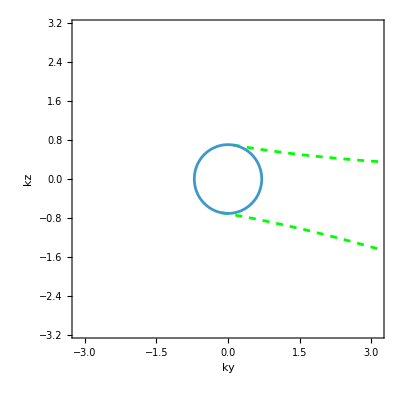

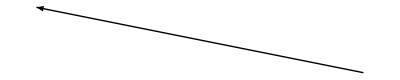

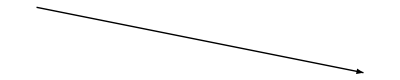

```mathematica
mu=0.5;lim=π;vp=1;vz=1;b=6;
(****{en->(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2, κr->ky-(kz vz)/(b vp), κi->0, a->0} ***)
c1=ContourPlot[(kz vz (2 b ky vp+(-1+b^2) kz vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Directive[Dashed,Green], PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},(ky-(kz vz)/(b vp))>0 ]]//Quiet;
(***********)
kx=0;
fs=ContourPlot[(kx^2+ky^2) vp^2+kz^2 vz^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},PlotLegends->Automatic];
Show[c1,fs]
(* {-(b vz)/vp,-(b vz)/vp} *)
g1=Graphics[Arrow[{{0,0},{-2 b vz ,2 vp }}]]
g2=Graphics[Arrow[{{0,0},-{-2 b vz ,2 vp }}]]
Clear[vp,vz,κr,κi,b,kx];
```

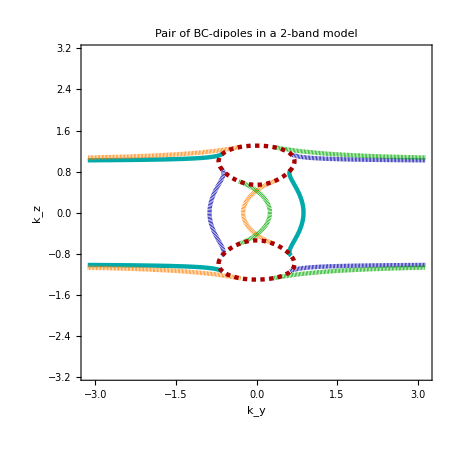

```mathematica
lim=π;th=0.007;mu=0.5;vp=1;vz=1;(*-0.3, -0.5, -2.5, 1, 20*);kw=1;
(**********)
b1v={-0.5, -2,0.5,2};
style={Directive[Darker[Cyan],Thickness[th]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]]};
(****************)
i=1;b=b1v[[i]];
c1=ContourPlot[((kz^2-kw^2)vz (2 b ky vp+(-1+b^2)(kz^2-kw^2) vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},(b vp ky-(kz^2-kw^2) vz)>0 ]]//Quiet;
(****************)
i=2;b=b1v[[i]];
c2=ContourPlot[((kz^2-kw^2) vz (2 b ky vp+(-1+b^2) (kz^2-kw^2) vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},(b vp ky-(kz^2-kw^2) vz)>0 ]]//Quiet;
(****************)
i=3;b=b1v[[i]];
c3=ContourPlot[((kz^2-kw^2) vz (2 b ky vp+(-1+b^2) (kz^2-kw^2) vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},(b vp ky-(kz^2-kw^2) vz)>0 ]]//Quiet;
(****************)
i=4;b=b1v[[i]];
	c4=ContourPlot[((kz^2-kw^2) vz (2 b ky vp+(-1+b^2) (kz^2-kw^2) vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},(b vp ky-(kz^2-kw^2) vz)>0 ]]//Quiet;
(***********)
kx=0;
fs=ContourPlot[(kx^2+ky^2) vp^2+(kz^2-kw^2)^2 vz^2==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];
pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"Pair of BC-dipoles in a 2-band model",20,FontFamily->"TexMaths Roman",Brown,Bold](**)];
leg=LineLegend[style,{b1v[[1]], b1v[[2]], b1v[[3]], b1v[[4]]},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
plt=Legended[GraphicsGrid[{{pl}},ImageSize->450],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["dipole2bandarc.pdf",Rasterize[plt],ImageResolution->100];
Clear[vp,vz,κr,κi,b,b1v,kw,kzt,kyt,kx,mu];
```

```mathematica
(*lim=π;th=0.007;mu=0.4;vp=1;vz=1;b=2;kw=1;kzt=kz^2-kw^2;
(**********)
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
(****************)
c1=ContourPlot[(kzt vz (2 b ky vp+(-1+b^2) kzt vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Directive[Orange,Thickness[th]],RegionFunction->Function[{ky,kz,z},(*(ky-(kzt vz)/(b vp))>0 *)((ky-(2kz(kz-kw) vz)/(b vp))>0 || (ky-(2kz(kz+kw) vz)/(b vp))>0 )&& (* for color-coding: *)Abs[kz]>0.9]]//Quiet;
(***********)
c2=ContourPlot[(kzt vz (2 b ky vp+(-1+b^2) kzt vz))/b^2==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Directive[Darker[Cyan],Thickness[th]],RegionFunction->Function[{ky,kz,z},(*(ky-(kzt vz)/(b vp))>0 *)((ky-(2kz(kz-kw) vz)/(b vp))>0 || (ky-(2kz(kz+kw) vz)/(b vp))>0 )&& (* for color-coding: *)Abs[kz]<0.9]]//Quiet;
(***********)
kx=0;
fs=ContourPlot[(kx^2+ky^2) vp^2+kzt^2 vz^2==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];
pl=Show[c1,c2,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"Pair of BC-dipoles in a 2-band model",20,FontFamily->"TexMaths Roman",Brown,Bold](**),ImagePadding->{{Automatic,Automatic},{90,Automatic}}(*{{left,right},{bottom,top}}*)]
Clear[vp,vz,κr,κi,b,kw,kzt,kyt,kx,mu];
SetDirectory[NotebookDirectory[]];
Export["dipole2bandarc.pdf",Rasterize[pl],ImageResolution->200];*)
```

## dispersion

```mathematica
lim=π;
ContourPlot3D[(kx^2+ky^2) +(kz^2 -1)^2==0.8,{kz,-lim,lim},{kx,-lim,lim},{ky,-lim,lim},AxesLabel->{kz,kx,ky}]
```

-Graphics3D-